# Computational Science

## Machine Learning for Physicists Project: Unsupervised and supervised analysis of protein sequences

This notebook is 100% human-made and has been created without the help of any LLM.

Paul Cousin

Université Paris Cité • Master’s Physics Of Complex Systems • 2025/2026

## Note to the reader

Cells colored in blue will be code cells.

Cells colored in pink will be text comments.

## Import and format data

```mathematica
formatData[s_String]:=Module[{string=s},
string//=StringSplit[#,">"]&;
string//=StringDelete[#,"\n"]&;
string//=StringReplace[#,"sequence_"~~x:NumberString~~" functional_"~~y:("true"|"false")~~z__~~WordBoundary:>x~~","~~y~~","~~z]&;string//=StringSplit[#,","]&;
string/.{x_,y_,z_}:>{ToExpression@x,y=="true",z}
];
```

formatData is a function that formats the content of the .faa files which is encapsulated in  and  in the following cell.

```mathematica
naturalSequences=formatData@;
artificialSequences=formatData@;
```

Here is an example of how a sequence is now formatted.

```mathematica
naturalSequences[[1]]
```

{1,True,-TSENPLLALREKISALDEKLLALLAERRELAVEVGKAKLLSHRPVRDIDRERDLLERLITLGK-AHHLDAHYITRLFQLIIEDSVLTQQALLQQH}

## Task 1: One-hot encoding of protein sequence data

Let’s encode our sequences using one-hot encoding.

```mathematica
characterMap={"A"->1,"C"->2,"D"->3,"E"->4,"F"->5,"G"->6,"H"->7,"I"->8,"K"->9,"L"->10,"M"->11,"N"->12,"P"->13,"Q"->14,"R"->15,"S"->16,"T"->17,"V"->18,"W"->19,"Y"->20};
```

```mathematica
oneHotEncode[seq_]:=SparseArray[If[#!="-",#->1,{}],20]&/@Replace[characterMap]/@StringPartition[seq,1];
```

```mathematica
naturalSequencesOneHot=Flatten/@SparseArray[oneHotEncode/@naturalSequences[[;;,3]]];
artificialSequencesOneHot=Flatten/@SparseArray[oneHotEncode/@artificialSequences[[;;,3]]];
```

All the sequences have been one-hot encoded in the SparseArray format, and reshaped to vector columns for the purpose of future computations.

## Task 2: Dimensional reduction and visualization of sequence space

Let’s compute the covariance matrix. Here, the number of features is not really the length of the vector but rather the original length of the sequence, since it is the maximum number of 1 that can appear in the vector. Our sequences are at most 96 base-pair long.

```mathematica
covarianceMatrixNatural=(#ᵀ.#)/95.&@naturalSequencesOneHot;
```

Using the first eigenvalues and eigenvectors of this covariance matrix, we can project our data on the two or three most meaningful axes. For this purpose we can use the Eigenvectors function which will return the first eigenvectors sorted by eigenvalues. Here we will compute only three.

```mathematica
eigenvectorsNatural=Eigenvectors[covarianceMatrixNatural,3];
```

```mathematica
projectedNaturalSequences=naturalSequencesOneHot.eigenvectorsNaturalᵀ;
```

To separate the functional and non-functional sequence, we need the indices corresponding to each.

```mathematica
funtionalNaturalIndices=Cases[naturalSequences,x_?(#[[2]]&):>x[[1]]];
nonFuntionalNaturalIndices=Complement[Range@Length@naturalSequences,funtionalNaturalIndices];
funtionalArtificialIndices=Cases[artificialSequences,x_?(#[[2]]&):>x[[1]]];
nonFuntionalArtificialIndices=Complement[Range@Length@artificialSequences,funtionalArtificialIndices];
```

Let’s plot the result, first in 2D.

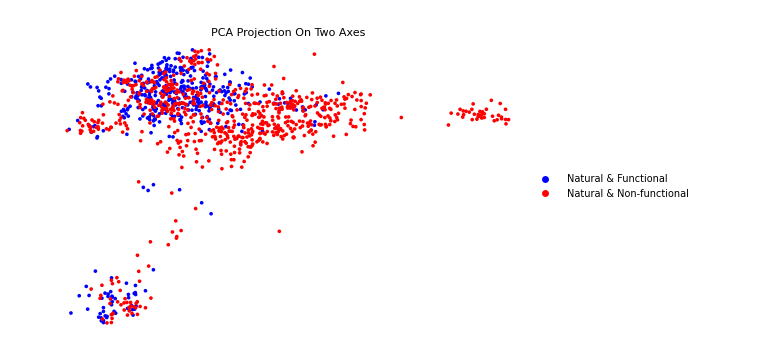

```mathematica
plotNatural2D=ListPlot[
projectedNaturalSequences[[#,;;2]]&/@{funtionalNaturalIndices,nonFuntionalNaturalIndices},
Axes->False,PlotRange->Full,ImageSize->Large,PlotStyle->{Blue,Red},PlotLabel->"PCA Projection On Two Axes",PlotLegends-> {"Natural & Functional","Natural & Non-functional"}]
```

The following 3D plot is interactive and can be manipulated.

```mathematica
plotNatural3D=ListPointPlot3D[
projectedNaturalSequences[[#]]&/@{funtionalNaturalIndices,nonFuntionalNaturalIndices},
Axes->False,PlotRange->Full,ImageSize->Large,PlotStyle->{Blue,Red},PlotLabel->"PCA Projection On Three Axes",PlotLegends-> {"Natural & Functional","Natural & Non-functional"}]
```

-Graphics3D-

Let’s now look at the artificial sequences projected on the previously computed vectors.

```mathematica
projectedArtificialSequences=artificialSequencesOneHot.eigenvectorsNaturalᵀ;
```

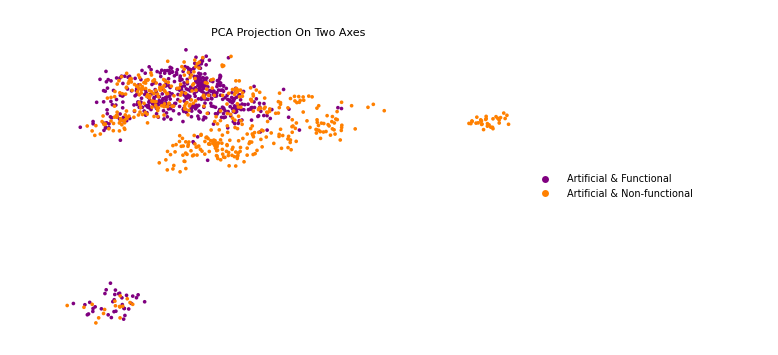

```mathematica
plotArtificial2D=ListPlot[projectedArtificialSequences[[#,;;2]]&/@{funtionalArtificialIndices,nonFuntionalArtificialIndices},
Axes->False,PlotRange->Full,ImageSize->Large,PlotStyle->{Purple,Orange},PlotLabel->"PCA Projection On Two Axes",PlotLegends-> {"Artificial & Functional","Artificial & Non-functional"}]
```

```mathematica
plotArtificial3D=ListPointPlot3D[projectedArtificialSequences[[#]]&/@{funtionalArtificialIndices,nonFuntionalArtificialIndices},
Axes->False,PlotRange->Full,ImageSize->Large,PlotStyle->{Purple,Orange},PlotLabel->"PCA Projection On Three Axes",PlotLegends-> {"Artificial & Functional","Artificial & Non-functional"}]
```

-Graphics3D-

To see the similarities more clearly let’s plot all sequences together.

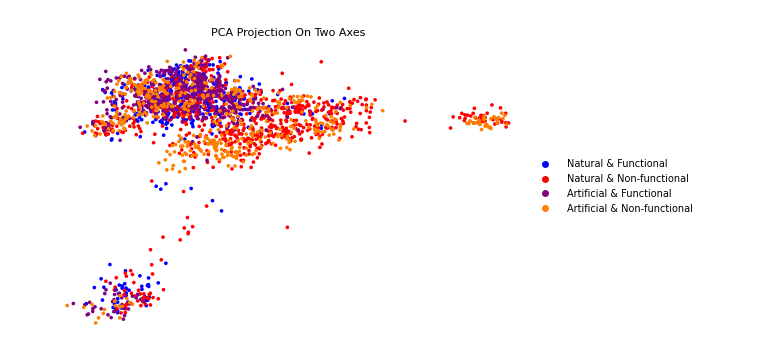

```mathematica
Show[{plotNatural2D,plotArtificial2D},PlotRange->All]
```

```mathematica
Show[{plotNatural3D,plotArtificial3D},PlotRange->All]
```

-Graphics3D-

In the case of both natural and artificial sequences, we see regions that are clearly non-functional and other regions in which a mixture of functional and non-functional sequences coexist.

## Task 3: Clustering sequence data